## 1.2 Subcritical pitchfork

### a)

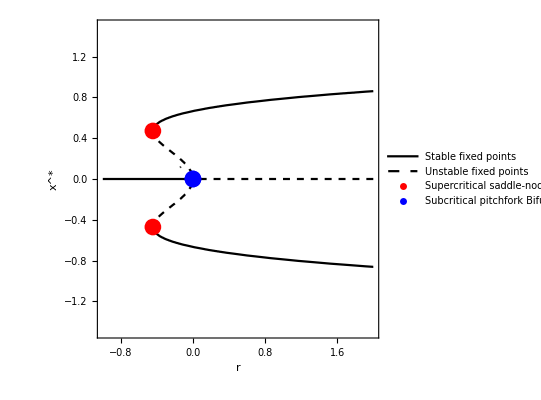

```mathematica
Clear["Global`*"]
ptsSaddle={{-4/9,(√2)/3},{-4/9,(-√2)/3}}; (*Bifurcation points are calculated in (b)*)
ptsPitch = {{0,0}};
λ=D[r x+4 x^3-9x^5,x];

(*Stable fixed point if λ < 0 and unstable fixed point if λ > 0*)
Show[
ContourPlot[{
ConditionalExpression[r x+4 x^3-9x^5,λ<0]==0,
ConditionalExpression[r x+4 x^3-9x^5,λ>0]==0},
{r,-1,2},{x,-1.5,1.5},
ContourStyle->{{Black},{Black,Dashed}},
FrameLabel->{Style["r",Black,Medium],Style["x^*",Black,Medium]},
RotateLabel->False,
LabelStyle->(FontSize->12),
PlotLegends->{"Stable fixed points","Unstable fixed points"}],
ListPlot[ptsSaddle, 
PlotLegends->{"Supercritical saddle-node Bifurcation"}, 
PlotStyle->{PointSize[0.03],Red}],
ListPlot[ptsPitch, 
PlotLegends->{"Subcritical pitchfork Bifurcation"},
PlotStyle->{PointSize[0.03],Blue}]
]
```